```mathematica
raw={{40,0.736578,0.741773,4.85531*10^-09},{39.5,0.726997,0.733467,5.58323*10^-15},{39,0.716267,0.724193,5.76588*10^-21},{38.5,0.704263,0.713864,3.08944*10^-23},{38,0.690841,0.702376,6.344*10^-29},{37.5,0.675834,0.689617,3.23875*10^-31},{37,0.659051,0.675462,3.28997*10^-33},{36.5,0.640264,0.659768,4.75236*10^-39},{36,0.619206,0.642381,4.17525*10^-45},{35.5,0.595559,0.623127,3.60344*10^-51},{35,0.568938,0.601811,1.70012*10^-53},{34.5,0.538882,0.578231,3.5612*10^-59},{34,0.504831,0.552172,2.78791*10^-65},{33.5,0.466117,0.523418,2.17314*10^-71},{33,0.421981,0.491779,1.64981*10^-77},{32.5,0.371701,0.457144,7.09858*10^-80},{32,0.315054,0.419572,1.524*10^-85},{31.5,0.253643,0.379313,6.16022*10^-88},{31,0.193102,0.337197,6.73026*10^-90},{30.5,0.14212,0.29454,9.29741*10^-96},{30,0.104974,0.253199,3.58396*10^-98},{29.5,0.0794086,0.215131,3.98401*10^-100},{29,0.0616612,0.181766,2.89821*10^-102},{28.5,0.0489734,0.15364,4.44816*10^-108},{28,0.0396145,0.130491,1.57526*10^-110},{27.5,0.0325224,0.111611,1.82471*10^-112},{27,0.0270381,0.0962101,1.23352*10^-114},{26.5,0.0227323,0.0835621,1.10038*10^-116},{26,0.0193029,0.0730765,1.44718*10^-122},{25.5,0.0165222,0.0643025,4.64208*10^-125},{25,0.0142146,0.0568829,5.25878*10^-127},{24.5,0.0122463,0.0505795,5.66892*10^-133},{24,0.0105147,0.0451393,1.64897*10^-135},{23.5,0.00893802,0.0404577,2.36657*10^-141},{23,0.00744504,0.0364058,9.98709*10^-148},{22.5,0.00595784,0.0328763,4.40503*10^-154},{22,0.00435288,0.0298139,1.87553*10^-160},{21.5,0.00223333,0.0271555,7.77329*10^-167},{21,1.08307*10^-07,0.0248508,2.16323*10^-169},{20.5,4.74813*10^-08,0.0228557,4.59692*10^-175},{20,1.05846*10^-10,0.0211175,1.56662*10^-181},{19.5,1.05215*10^-13,0.0196063,5.89465*10^-188},{19,5.91359*10^-17,0.0182832,1.51326*10^-190},{18.5,2.13453*10^-20,0.017115,1.84041*10^-192},{18,5.36015*10^-24,0.0160771,1.20725*10^-198},{17.5,6.81615*10^-25,0.0151469,3.73666*10^-205},{17,1.15535*10^-28,0.014307,1.20893*10^-211},{16.5,1.28698*10^-32,0.0135412,3.74168*10^-218},{16,1.15859*10^-36,0.0128393,8.52129*10^-221},{15.5,8.59185*10^-41,0.0121912,1.6734*10^-226},{15,5.54552*10^-42,0.0115886,3.16679*10^-229},{14.5,4.3716*10^-43,0.0110254,7.19408*10^-235},{14,2.71521*10^-47,0.010496,1.48225*10^-241},{13.5,1.29563*10^-48,0.00999596,3.22091*10^-244},{13,8.42732*10^-50,0.0095215,3.82598*10^-246},{12.5,3.73568*10^-54,0.00906937,2.34686*10^-252},{12,1.37141*10^-55,0.0086368,4.65403*10^-259},{11.5,7.64362*10^-57,0.00822142,8.64867*10^-262},{11,2.56402*10^-61,0.00782113,7.54892*10^-264},{10.5,7.41852*10^-63,0.00743408,2.83628*10^-266},{10,3.68934*10^-64,0.00705585,4.43034*10^-272}};
```

```mathematica
makeSeries:=Table[Table[{raw[[j]][[1]],raw[[j]][[1+i]]},{j,1,Length[raw]}],{i,1,3}]
```

```mathematica
table[pairs_]:=Grid[Transpose[pairs],Spacings->{1,0}];
```

```mathematica
fm2[name_String,size_,opacity_]:=ResourceFunction["PolygonMarker"][name,Offset@size,{Dynamic@EdgeForm[{CurrentValue["Color"],Opacity[opacity]}],Dynamic@FaceForm@Lighter[CurrentValue["Color"],0.75]}];
```

```mathematica
markers={fm2["Square",0.4*20,1.0],fm2["Diamond",0.4*17,1.0],fm2["ThreePointedStar",0.4*11,1.0]};
```

```mathematica
ν=0.35
```

0.35

```mathematica
Romero[w_]:=18.2(1-ν)Sqrt[1+ν]+14.5 w
```

```mathematica
Romero[0.5]
```

20.9952

```mathematica
makePlot[romero_]:=Show[ListPlot[makeSeries,PlotMarkers->markers,Joined->True,PlotRange->{-.002,0.1},Frame->True,ImageSize->Large,FrameTicksStyle->Directive[14],PlotLegends->Placed[PointLegend[ConstantArray["",3],LabelStyle->20,LegendLayout->table,LegendMargins->{{0,0},{-30,0}},LegendMarkerSize->{80,50}],Above]],Graphics[{Black,Thick,Dotted,InfiniteLine[{romero,0},{0,1}]}]]
```

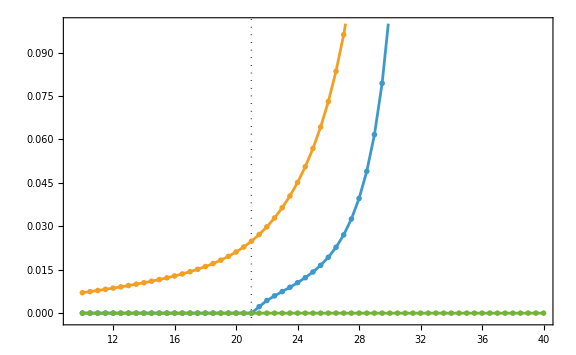

```mathematica
plt = makePlot[Romero[0.5]]
```

```mathematica
Export[NotebookDirectory[]<>"W-0.5.pdf",plt]
```

C:\Users\evoug\Documents\Projects\lateralbuckling\plots\W-0.5.pdf